# ECH 28GHz Perpendicular Stratification, B(x)ẑ Linear gradient in |B(x)|: 0.5T ≤ B ≤ 1.5T

## Open Additional files:

## Get dispersion routines by evaluating Plasma_Dispersion.nb Get plotting and printing routines by evaluating PlotPack.nb Note: Slab profile models defined in initialization cells at the bottom of this notebook. Note: Input parameters set in initialization cells below case runs.

### Plot Real and Imaginary parts of n_x^2 from 4nd order cold plasma dispersion relation (Fast and Slow roots)

α =  0.30849,  nz = 0.5

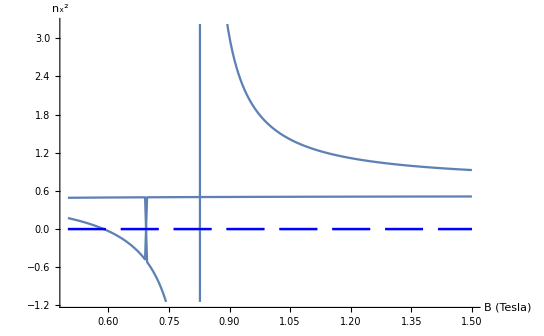

dataSet=Perpendicular Stratification 28HHz, grad B

xProfileMin=0.5

xProfileMax=1.5

nXmin=3.×10^18

nXmax=3.×10^18

BXmin=0.5

BXmax=1.5

freq=28000.

nz=0.5

etaList={0.,1.,0.,0.,0.}

xmin=0.5

xmax=1.5

```mathematica
nPerp2FS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
 nxSqColdDisFS[freq,ne,b,nz,etaList]];
ntFS=Table[Flatten[{x,nPerp2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[ntFS]⟦1⟧,Transpose[ntFS]⟦2⟧}];
nS=Transpose[{Transpose[ntFS]⟦1⟧,Transpose[ntFS]⟦3⟧}];
g1=PPComplexListPlot[nF,"B (Tesla)","n_x^2"];
g2=PPComplexListPlot[nS,"B (Tesla)","n_x^2"];
Show[{g1,g2},PlotRange->All]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of n_x^2 from 4nd order cold plasma dispersion relation (Plus and Minus roots)

α =  0.30849,  nz = 0.5

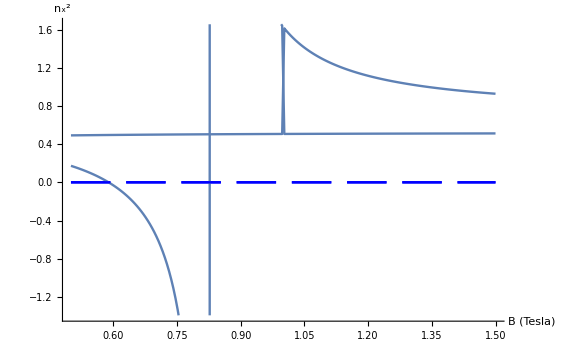

dataSet=Perpendicular Stratification 28HHz, grad B

xProfileMin=0.5

xProfileMax=1.5

nXmin=3.×10^18

nXmax=3.×10^18

BXmin=0.5

BXmax=1.5

freq=28000.

nz=0.5

etaList={0.,1.,0.,0.,0.}

xmin=0.5

xmax=1.5

```mathematica
nPerp2PM[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
 nxSqColdDisPM[freq,ne,b,nz,etaList]];
ntPM=Table[Flatten[{x,nPerp2PM[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nP=Transpose[{Transpose[ntPM]⟦1⟧,Transpose[ntPM]⟦2⟧}];
nM=Transpose[{Transpose[ntPM]⟦1⟧,Transpose[ntPM]⟦3⟧}];
g1=PPComplexListPlot[nP,"B (Tesla)","n_x^2"];
g2=PPComplexListPlot[nM,"B (Tesla)","n_x^2"];
Show[{g1,g2},PlotRange->All]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of n_x from 4nd order cold plasma dispersion relation (Plus and Minus roots)

α =  0.30849,  nz = 0.5

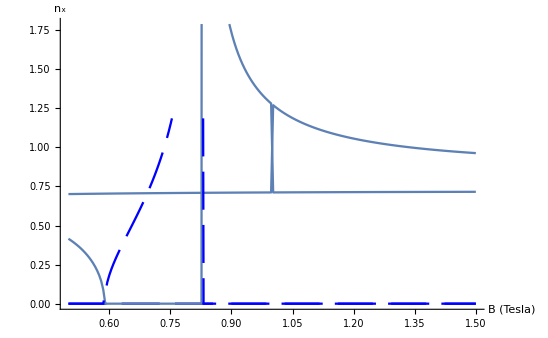

dataSet=Perpendicular Stratification 28HHz, grad B

xProfileMin=0.5

xProfileMax=1.5

nXmin=3.×10^18

nXmax=3.×10^18

BXmin=0.5

BXmax=1.5

freq=28000.

nz=0.5

etaList={0.,1.,0.,0.,0.}

xmin=0.5

xmax=1.5

```mathematica
nPerpPM[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
nxColdDisPM[freq,ne,b,nz,etaList]];
ntPM=Table[Flatten[{x,nPerpPM[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nP=Transpose[{Transpose[ntPM]⟦1⟧,Transpose[ntPM]⟦2⟧}];
nM=Transpose[{Transpose[ntPM]⟦1⟧,Transpose[ntPM]⟦3⟧}];
g1=PPComplexListPlot[nP,"B (Tesla)","n_x"];
g2=PPComplexListPlot[nM,"B (Tesla)","n_x"];
Show[{g1,g2},PlotRange->All]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of n_x from 4nd order cold plasma dispersion relation (Fast and Slow roots)

α =  0.30849,  nz = 0.5

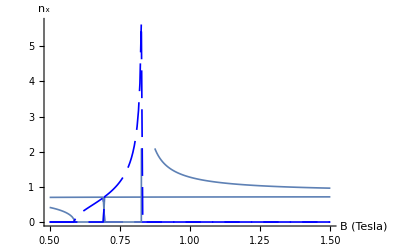

dataSet=Perpendicular Stratification 28HHz, grad B

xProfileMin=0.5

xProfileMax=1.5

nXmin=3.×10^18

nXmax=3.×10^18

BXmin=0.5

BXmax=1.5

freq=28000.

nz=0.5

etaList={0.,1.,0.,0.,0.}

xmin=0.5

xmax=1.5

```mathematica
nPerpFS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
nxColdDisFS[freq,ne,b,nz,etaList]];
ntFS=Table[Flatten[{x,nPerpFS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[ntFS]⟦1⟧,Transpose[ntFS]⟦2⟧}];
nS=Transpose[{Transpose[ntFS]⟦1⟧,Transpose[ntFS]⟦3⟧}];
g1=PPComplexListPlot[nF,"B (Tesla)","n_x"];
g2=PPComplexListPlot[nS,"B (Tesla)","n_x"];
Show[{g1,g2},PlotRange->All]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

## Change to exactly perpendicular propagation n_z=0

```mathematica
nz=0.;
```

### Plot Real and Imaginary parts of n_x^2 from 4nd order cold plasma dispersion relation (Fast and Slow roots)

α =  0.30849,  nx = 0

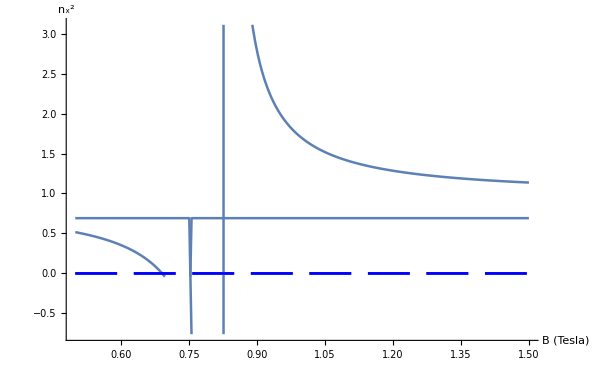

dataSet=Perpendicular Stratification 28HHz, grad B

xProfileMin=0.5

xProfileMax=1.5

nXmin=3.×10^18

nXmax=3.×10^18

BXmin=0.5

BXmax=1.5

freq=28000.

nz=0.

etaList={0.,1.,0.,0.,0.}

xmin=0.5

xmax=1.5

```mathematica
nPerp2FS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
 nxSqColdDisFS[freq,ne,b,nz,etaList]];
ntFS=Table[Flatten[{x,nPerp2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[ntFS]⟦1⟧,Transpose[ntFS]⟦2⟧}];
nS=Transpose[{Transpose[ntFS]⟦1⟧,Transpose[ntFS]⟦3⟧}];
g1=PPComplexListPlot[nF,"B (Tesla)","n_x^2"];
g2=PPComplexListPlot[nS,"B (Tesla)","n_x^2"];
Show[{g1,g2},PlotRange->All]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of n_x^2 from 4nd order cold plasma dispersion relation (Plus and Minus roots)

α = 0.30849,  nx = 0.0

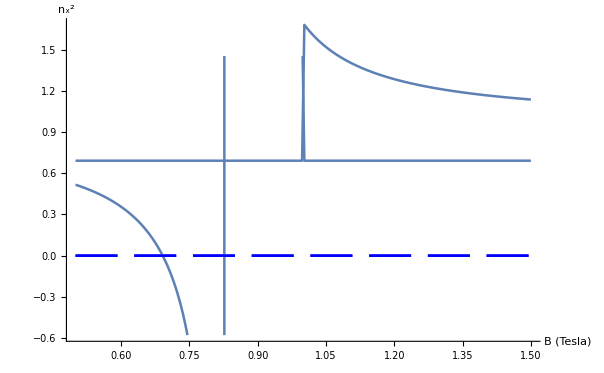

dataSet=Perpendicular Stratification 28HHz, grad B

xProfileMin=0.5

xProfileMax=1.5

nXmin=3.×10^18

nXmax=3.×10^18

BXmin=0.5

BXmax=1.5

freq=28000.

nz=0.

etaList={0.,1.,0.,0.,0.}

xmin=0.5

xmax=1.5

```mathematica
nPerp2PM[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
 nxSqColdDisPM[freq,ne,b,nz,etaList]];
ntPM=Table[Flatten[{x,nPerp2PM[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nP=Transpose[{Transpose[ntPM]⟦1⟧,Transpose[ntPM]⟦2⟧}];
nM=Transpose[{Transpose[ntPM]⟦1⟧,Transpose[ntPM]⟦3⟧}];
g1=PPComplexListPlot[nP,"B (Tesla)","n_x^2"];
g2=PPComplexListPlot[nM,"B (Tesla)","n_x^2"];
Show[{g1,g2},PlotRange->All]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of n_x from 4nd order cold plasma dispersion relation (Plus and Minus roots)

α =  0.30849,  nx = 0.

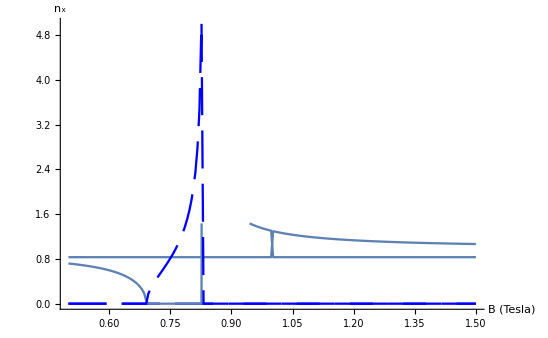

dataSet=Perpendicular Stratification 28HHz, grad B

xProfileMin=0.5

xProfileMax=1.5

nXmin=3.×10^18

nXmax=3.×10^18

BXmin=0.5

BXmax=1.5

freq=28000.

nz=0.

etaList={0.,1.,0.,0.,0.}

xmin=0.5

xmax=1.5

```mathematica
nPerpPM[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
nxColdDisPM[freq,ne,b,nz,etaList]];
ntPM=Table[Flatten[{x,nPerpPM[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nP=Transpose[{Transpose[ntPM]⟦1⟧,Transpose[ntPM]⟦2⟧}];
nM=Transpose[{Transpose[ntPM]⟦1⟧,Transpose[ntPM]⟦3⟧}];
g1=PPComplexListPlot[nP,"B (Tesla)","n_x"];
g2=PPComplexListPlot[nM,"B (Tesla)","n_x"];
Show[{g1,g2},PlotRange->{0.,5.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of n_x from 4nd order cold plasma dispersion relation (Fast and Slow roots)

α =  0.30849,  nx = 0.

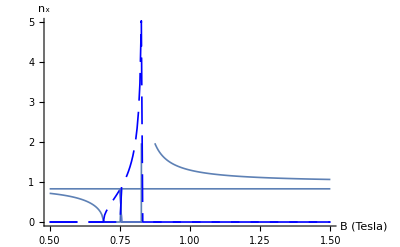

dataSet=Perpendicular Stratification 28HHz, grad B

xProfileMin=0.5

xProfileMax=1.5

nXmin=3.×10^18

nXmax=3.×10^18

BXmin=0.5

BXmax=1.5

freq=28000.

nz=0.

etaList={0.,1.,0.,0.,0.}

xmin=0.5

xmax=1.5

```mathematica
nPerpFS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
nxColdDisFS[freq,ne,b,nz,etaList]];
ntFS=Table[Flatten[{x,nPerpFS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[ntFS]⟦1⟧,Transpose[ntFS]⟦2⟧}];
nS=Transpose[{Transpose[ntFS]⟦1⟧,Transpose[ntFS]⟦3⟧}];
g1=PPComplexListPlot[nF,"B (Tesla)","n_x"];
g2=PPComplexListPlot[nS,"B (Tesla)","n_x"];
Show[{g1,g2},PlotRange->{0.,5.}]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

## Plot Profiles

```mathematica
Plot[nprof[x],{x,xmin,xmax}]
```

-Graphics-

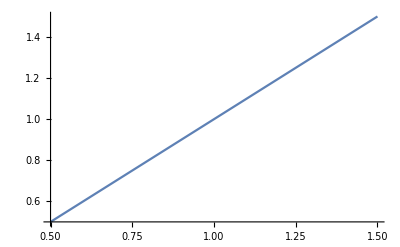

```mathematica
Plot[bprof[x],{x,xmin,xmax}]
```

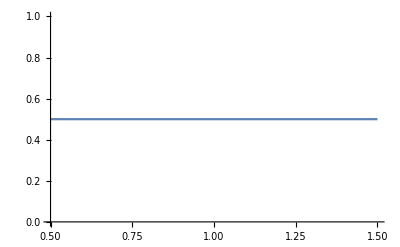

```mathematica
Plot[tprof[x],{x,xmin,xmax}]
```

```mathematica
αHcut[BXmax,freq, nz,1]
```

1.00015

## Initialization

## Set Perpendicular Stratification Parameters

### Geometric Parameters

```mathematica
xProfileMin=0.5;
xProfileMax=1.5;
nXmin=.03  10^20; (* α=0.30849 at 28GHz*)
nXmax=.03  10^20;
BXmin=0.5;
BXmax=1.5;
(* N.B. For Linear slab model Te Xmin and Te Xmax are defined here.  TList below gives the ratio of various Ti to Te  *)
TXmin=0.5;
TXmax=0.5;
```

### RF Parameters

```mathematica
freq=28.*10^3;
c=2.9979 10^8;
k0=(2 N[π] freq 10^6)/c
nz  =0.5;
kz= nz * k0
```

586.841

293.421

### Plasma Parameters

```mathematica
etaList=Table[0.,{i,1,5}];
etaList⟦1⟧=0.;etaList⟦2⟧=1.0;etaList⟦3⟧=0.; (* ion species is deuterium *)
etaList⟦4⟧=0.;etaList⟦5⟧=0.;

(* N.B. For Linear slab model Te Xmin and Te Xmax are defined above.  TList here gives the ratio of various Ti to Te (i.e. TList[[1]] = 1.0 always)  *)
TList=Table[0.,{i,1,6}];
TList⟦1⟧=1.0;TList⟦2⟧=1.0;
TList⟦3⟧=0. ;TList⟦4⟧=0.;
TList⟦5⟧=0.;TList⟦6⟧=0.;

modelList =Table[0,{i,1,6}];
modelList[[1]]=1; modelList[[2]]=1
modelList[[3]]=0; modelList[[4]]=0;
modelList[[5]]=0; modelList[[6]]=0;

nminList=Table[0.,{i,1,6}];
nminList⟦1⟧=-1;nminList⟦2⟧=-2;
nminList⟦3⟧=-2;nminList⟦4⟧=-2;
nminList⟦5⟧=-2;nminList⟦6⟧=-2;

nmaxList=Table[0.,{i,1,6}];
nmaxList⟦1⟧=1;nmaxList⟦2⟧=2;
nmaxList⟦3⟧=2;nmaxList⟦4⟧=2;
nmaxList⟦5⟧=2;nmaxList⟦6⟧=2;
```

1

### Plot Parameters

```mathematica
dataSet="Perpendicular Stratification 28HHz, grad B";
xmin=xProfileMin;
xmax=xProfileMax;
nPoints=200;
```

## Magnetic field,Density and Temperature Profiles

```mathematica
bprof[x_]:=If[Abs[(BXmax-BXmin)/BXmax]>10^-6,BXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(BXmax-BXmin),BXmin];
```

```mathematica
nprof[x_]:=If[Abs[(nXmax-nXmin)/nXmax]>10^-6,nXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(nXmax-nXmin),nXmin];
```

```mathematica
tprof[x_]:=If[Abs[(TXmax-TXmin)/TXmax]>10^-6,TXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(TXmax-TXmin),TXmin];
```

```mathematica
αHcut[B_,freq_, nz_,sgn_]:=(1-nz^2)×(1+sgn*2.79926 B/freq)
```